# Liver slices MFA from text format

NOT FINISHED

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`MetabolicNetwork`Common`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

## Import model

### Importing from Openflux format

```mathematica
Clear[NilssonLab`OpenFLUX`Private`importMetabolicNetwork]
```

```mathematica
net=OpenFLUXImport["liver-model-2_openflux.txt"]
```

<MetabolicNetwork, 89 reactions>

## Check against DB model

### Check against network from database

```mathematica
<<NilssonLab`MetabolicNetwork`DB`
```

```mathematica
dbNet=NetworkFromDB["liver-model-2"]
```

<MetabolicNetwork, 89 reactions>

```mathematica
dbNet==net
```

True

### Get atom map from database

All atom transitions for reactions in model

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
```

```mathematica
atomMap=RemoveUnreachable[net,atomMap];
Length[atomMap]
```

89

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]/.{{ri_Integer,s_List,p_List}:>{Reactions[net]⟦ri⟧,Union[Metabolite/@First/@s],Union[Metabolite/@First/@p]}}
```

{}

```mathematica
AtomList[atomMap]//Length
```

282

```mathematica
Total[Length/@EductList/@atomMap]
```

333

```mathematica
CheckAtomMap[atomMap]
```

{}

Verify that atom map matches stoichimetry

```mathematica
Block[{S,mr,t,mi,coeff},
S=Stoichiometry[net];
mr=Dispatch[Thread[Rule[Metabolites[net],Range[Length[Metabolites[net]]]]]];
Flatten[Position[Table[
t=Join[
Map[First[SortBy[#,Last]]&,GatherBy[
EductList[atomMap⟦j⟧]/.{{Atom[m_Metabolite,__],c_}:>{m/.mr,-c}},
First]],
Map[Last[SortBy[#,Last]]&,GatherBy[
ProductList[atomMap⟦j⟧]/.{{Atom[m_Metabolite,__],c_}:>{m/.mr,c}},
First]]];
If[Length[t]>0,
{mi,coeff}=Transpose[t];
Normal[S⟦mi,j⟧==coeff],
(* else *)
True],
{j,Length[Reactions[net]]}],
False]]]
```

{}

```mathematica
TableForm/@atomMap⟦27⟧
```

AtomMap[{},{}]

```mathematica
TableForm/@atomMap⟦26⟧
```

AtomMap[<accoa_c(C1)> | 1
<accoa_c(C12)> | 1,<acrn_c(C1)> | 1
<acrn_c(C7)> | 1]

```mathematica
Cases[AtomList[atomMap],Atom[Metabolite["fum",__],__]]
```

{<fum_c(C1)>,<fum_c(C2)>,<fum_c(C3)>,<fum_c(C4)>,<fum_m(C1)>,<fum_m(C2)>,<fum_m(C3)>,<fum_m(C4)>}

Reactions with no atom mappings.

```mathematica
Pick[Reactions[net],EductArity/@atomMap,0]
```

{<Reaction ADK1>,<Reaction ATPS4m>,<Reaction ATPtm(rev)>,<Reaction CELLWORK>,<Reaction CRNtim>,<Reaction CYOOm>,<Reaction CYOR-u10m>,<Reaction H2Oter>,<Reaction H2Otm(rev)>,<Reaction Htm2(rev)>,<Reaction NADH2-u10m>,<Reaction NADH_REDOX>,<Reaction NDPK1>,<Reaction NH4tm(rev)>,<Reaction O2tm>,<Reaction PIt2m>,<Reaction PIter>,<Reaction PPA>}

```mathematica
Length[%]
```

18

Metabolites without (some) atom information (+ sink)

```mathematica
MetaboliteShortName/@Complement[Metabolites[net],Metabolite/@AtomList[atomMap]]//Sort
```

{adp_c,adp_m,amp_c,atp_c,atp_m,coa_c,coa_m,crn_c,crn_m,energy_c,ficytC_m,focytC_m,gdp_c,gtp_c,h2o_c,h2o_m,h2o_r,h_c,h_ims_m,h_m,nad_c,nadh_c,nadh_m,nad_m,nh4_c,nh4_m,o2_c,o2_m,pi_c,pi_m,pi_r,ppi_c,q10h2_m,q10_m,thf_c}

```mathematica
Length[%]
```

35

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

35

### Measured MIDs

```mathematica
<<"metList-mids_liverslices-june.mx"
```

NOTE: not all of these are well measured

```mathematica
TableForm[metList,TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4
1 | glc-D | -1 | 3.2 | 3.5
2 | ala-L | 1 | 3.25 | 3.45
3 | arg-L | 1 | 5.5 | 6.1
4 | asn-L | 1 | 3.5 | 3.7
5 | asp-L | 1 | 3.55 | 3.85
6 | Lcystin | 1 | 3.6 | 4.
7 | gln-L | 1 | 3.4 | 3.7
8 | glu-L | -1 | 3.4 | 3.75
9 | gly | 1 | 3.6 | 3.8
10 | his-L | 1 | 3. | 4.2
11 | leu-L | 1 | 2.2 | 2.7
12 | lys-L | 1 | 5.4 | 5.8
13 | met-L | 1 | 2.4 | 2.55
14 | phe-L | 1 | 2.1 | 2.3
15 | pro-L | 1 | 2.8 | 3.
16 | ser-L | 1 | 3.6 | 3.8
17 | thr-L | 1 | 3.15 | 3.35
18 | trp-L | 1 | 2.6 | 2.8
19 | tyr-L | 1 | 2.8 | 3.2
20 | val-L | 1 | 2.75 | 2.85
21 | cit | -1 | 0 | 6
22 | mal-L | -1 | 3.8 | 4.15
23 | g6p | -1 | 3.85 | 4.35
24 | g3p | -1 | 3.6 | 4.
25 | r5p | -1 | 3.5 | 4.5
26 | udpg | -1 | 4 | 4.3
27 | crn | 1 | 2.9 | 3.2
28 | creat | 1 | 3.35 | 3.55
29 | orn | 1 | 4.95 | 5.3
30 | citr-L | 1 | 3.6 | 3.9
31 | gudac | 1 | 3.65 | 3.85
32 | adma | 1 | 4.56 | 4.98
33 | argsuc | 1 | 4 | 4.2
34 | glyc3p | -1 | 3.6 | 3.85
35 | acrn | 1 | 2.2 | 2.5
36 | acnt | 1 | 0 | 6
37 | akg | -1 | 0 | 6

Index of measurements used for MFA
NOTE: g6p seems fishy, dropped it ...

```mathematica
measuredIndex=ReindexList[
{"glc-D","ala-L","arg-L","asp-L","gln-L","glu-L","gly","ser-L","mal-L","g3p","acrn","glyc3p","orn","citr-L"},
metList⟦All,1⟧]
```

{1,2,3,5,7,8,9,16,22,24,35,34,29,30}

```mathematica
metList⟦measuredIndex,1⟧
```

{glc-D,ala-L,arg-L,asp-L,gln-L,glu-L,gly,ser-L,mal-L,g3p,acrn,glyc3p,orn,citr-L}

TODO: acrn must be deconvoluted to discount natural 13C in carnitine moiety
For now we just take the 3 first MIs and renormalize

```mathematica
mids["acrn"]=Block[{t},
t=Take[mids["acrn"],3];
Map[#/Total[t,{1}]&,t]];
```

```mathematica
mids["glc-D"]
```

{{{{0.940693,0.943013,0.942653},{0.937111,0.936674,0.936083},{0.939444,0.937467,0.944314},{0.0410825,0.0449763,0.0534016},{0.939943,0.936906,0.937951},{0.478244,0.435955,0.476408}},{{0.939628,0.941932,0.939797},{0.940515,0.939495,0.936938},{0.943084,0.939197,0.946015},{0.233596,0.266391,0.286962},{0.938904,0.938267,0.938814},{0.459452,0.553855,0.456498}}},{{{0.0593074,0.0569867,0.057347},{0.062889,0.0633263,0.0639167},{0.0605556,0.0625327,0.055686},{0.00740826,0.00535353,0.00312287},{0.0600571,0.0630937,0.0620494},{0.0461622,0.0398734,0.045719}},{{0.0597644,0.0580683,0.0602032},{0.0594855,0.0605053,0.0630619},{0.0569162,0.060803,0.0539852},{0.0175199,0.0184144,0.0189783},{0.0610957,0.0617326,0.0611858},{0.0290035,0.0367027,0.0306713}}},{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.00824849,0.00217332,0.00256568},{0.,0.,0.},{0.0188211,0.0189979,0.019264}},{{0.000607666,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.00227531,0.00230168,0.000706079},{0.,0.,0.},{0.00213419,0.00201087,0.00423882}}},{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.0240027,0.0109107,0.0157371},{0.,0.,0.},{0.0267711,0.0220147,0.0256758}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.00951432,0.0110786,0.00901148},{0.,0.,0.},{0.00611335,0.00808635,0.00543178}}},{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.0123227,0.00551282,0.0026457},{0.,0.,0.},{0.00707886,0.00784299,0.00637485}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.000371881,0.000859965,0.000344234},{0.,0.,0.},{0.,0.000722018,0.}}},{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.0568469,0.0540329,0.0550197},{0.,0.,0.},{0.0259266,0.0266056,0.0237415}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.0414986,0.0387083,0.0359975},{0.,0.,0.},{0.0281817,0.0225692,0.0269677}}},{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.850089,0.87704,0.867507},{0.,0.,0.},{0.396996,0.44871,0.402817}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.695224,0.662246,0.648},{0.,0.,0.},{0.475115,0.376054,0.476192}}}}

### Measured fluxes

Average values from the two experiments, from relative abundance data for known medium components

```mathematica
BoundaryFluxNames[bnet]
```

{2mop_IN,ac_IN,ala-L_IN,arg-L_IN,asp-L_IN,co2_IN,energy_IN,glc-D_IN,gln-L_IN,glucys_IN,gly_IN,glyc_IN,glycogen_IN,h_IN,h2o_IN,nh4_IN,o2_IN,pi_IN,prot_ala_IN,prot_arg_IN,ser-L_IN,arg-L_OUT,asp-L_OUT,co2_OUT,energy_OUT,glc-D_OUT,glu-L_OUT,gthrd_OUT,h_OUT,h2o_OUT,lac-L_OUT,nh4_OUT,pi_OUT,ser-L_OUT,urea_OUT}

We don’t have a value for glucose, but need something to prevent infinite uptake ...

```mathematica
measuredFluxes={"ala-L_IN"->1.91,"asp-L_IN"->0.55,"arg-L_IN"->0.23,"glc-D_IN"->1.0,"gln-L_IN"->4.10,"gly_IN"->1.54,"ser-L_IN"->0.22,"asp-L_OUT"->0.1,"glu-L_OUT"->0.54};
```

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{89,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

73

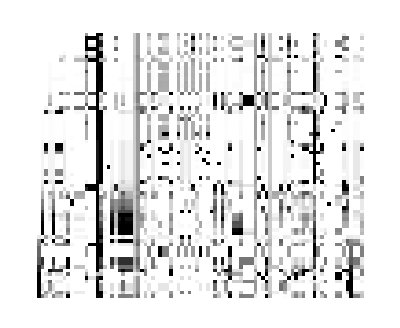

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

#### Blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]
```

{{<Reaction ACONTm(rev)>,cit_m <=> icit_m},{<Reaction ASPTAm(rev)>,glu-L_m + oaa_m <=> akg_m + asp-L_m},{<Reaction ATPtm(rev)>,adp_c + atp_m <=> adp_m + atp_c},{<Reaction G3PD1(rev)>,glyc3p_c + nad_c <=> dhap_c + h_c + nadh_c},{<Reaction GHMT2r(rev)>,ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c},{<Reaction GLUNm(rev)>,gln-L_m + h2o_m <=> glu-L_m + nh4_m},{<Reaction ICDHxm(rev)>,icit_m + nad_m <=> akg_m + co2_m + nadh_m},{<Reaction LDH_L(rev)>,h_c + nadh_c + pyr_c <=> lac-L_c + nad_c},{<Reaction MDHm(rev)>,mal-L_m + nad_m <=> h_m + nadh_m + oaa_m},{<Reaction PYRt2m(rev)>,pyr_c <=> pyr_m}}

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[energy,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[pi,Output,Boundary]}

## Symmetry

IMPORTANT: equivalent fragments must always be listed in sorted order, so that they are identified as same by Equals, Tally, etc

### Symmetry generation functions

This generates n-degree rotational symmetry given a list of rotations
{a_1→a_2→... →a_n, b_1→b_2→... →b_n...}
and the list of all atoms in the molecule. The equivalent EMUs are, for each subset of the rotating atoms, collection of atoms after rotating 1,2,3 ... n times.

```mathematica
Clear[RotationalSymmetry]
```

This generates replacement rules

```mathematica
RotationalSymmetry[rgroups:{{_Integer..}..}]:=
Table[
Thread[Rule[Flatten[rgroups],Join@@Table[RotateLeft[r,k],{r,rgroups}]]],
{k,Length[First[rgroups]]}]
```

Apply replacement rules to generate equivalent atom sets (EMUs). This produces only distinct subsets.

```mathematica
RotationalSymmetry[atomList:{_Integer..},rl:{{_Rule..}..}]:=
DeleteDuplicates[Table[Sort[Replace[atomList,r,1]],{r,rl}]]
```

With an empty rule list, we return the atom set itself

```mathematica
RotationalSymmetry[atomList:{_Integer..},{}]:={atomList}
```

```mathematica
RotationalSymmetry[atomList:{_Integer..},rgroups:{_List..}]:=
RotationalSymmetry[atomList,RotationalSymmetry[rgroups]]
```

### Generate equivalent EMUs

```mathematica
symmetry={"fum"->{{1,2},{3,4}},"succ"->{{1,2},{3,4}}}
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

Generate EMU symmetry maps

This function uses the symmetry list to generate equivalent EMUs as needed. If no symmetry rules are available for a given metabolite, we return back the EMU unchanged.

Currently this only works for carbon (1-element) EMUs

```mathematica
emuEquiv[EMU[Metabolite[metId_,c_,x_],{{al_}}]]:=
Block[{rl,el,nAtoms,rgroups},
rgroups=metId/.symmetry/.{_String->{}};
EMU[Metabolite[metId,c,x],Sort[List/@RotationalSymmetry[al,rgroups]]]]
```

If we already have a list of equivalent EMUs, we assume it is complete

```mathematica
emuEquiv[e:EMU[_Metabolite,al_List/;Length[al]>1]]:=e
```

```mathematica
emuEquiv[EMU[Metabolite["succ","Cytosol","Internal"],{{{1,2,3}}}]]
```

<succ_c{(123)|(124)}>

## EMU model

We generate a carbon-only EMU network by specifying only carbon fragments as targets

This needs to be done only once, defined by the target set.

### Map measured peaks to model metabolites targets

List of all target EMUs matching measured MIDs, in any compartment

```mathematica
targets=Block[{emus},
emus=MetaboliteEMUs[atomMap,{"C"}];
Flatten[Table[
Cases[emus,EMU[Metabolite[m,_,_],__]],
{m,metList⟦measuredIndex,1⟧}]]]
```

{<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<ser-L_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<g3p_c{(123)}>,<acrn_c{(17)}>,<acrn_m{(17)}>,<glyc3p_c{(123)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>}

```mathematica
Length[targets]
```

22

Create (measurements x targets) mixing matrix

```mathematica
emuMixing=SparseArray[
Flatten[Table[
Thread[Rule[Thread[
{i,Flatten[Position[targets,EMU[Metabolite[Alternatives@@metList⟦measuredIndex⟦i⟧,1⟧,_,_],__]]]}],1]],
{i,Length[measuredIndex]}]],
{Length[measuredIndex],Length[targets]}]
```

SparseArray[<22>, {14, 22}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/((Total/@emuMixing)/.{0->1})];
```

Zero rows in this matrix occur for unused MID data (metabolite not in the model)

```mathematica
Total/@emuMixing
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

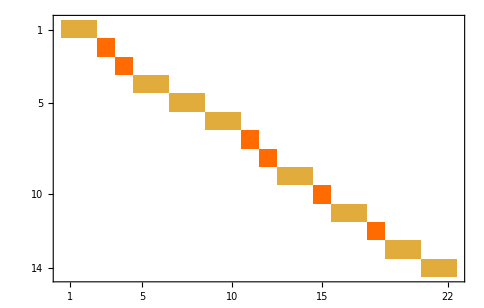

```mathematica
MatrixPlot[emuMixing]
```

Verify that all measured MIDs map to network EMUs

```mathematica
Flatten[Position[Total/@emuMixing,0]]
```

{}

List of measurement-to-target map

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixing];
Transpose[{metList⟦measuredIndex⟦ij⟦All,1⟧⟧,1⟧,targets⟦ij⟦All,2⟧⟧}]]//TableForm
```

glc-D | <glc-D_c{(123456)}>
glc-D | <glc-D_r{(123456)}>
ala-L | <ala-L_c{(123)}>
arg-L | <arg-L_c{(123456)}>
asp-L | <asp-L_c{(1234)}>
asp-L | <asp-L_m{(1234)}>
gln-L | <gln-L_c{(12345)}>
gln-L | <gln-L_m{(12345)}>
glu-L | <glu-L_c{(12345)}>
glu-L | <glu-L_m{(12345)}>
gly | <gly_c{(12)}>
ser-L | <ser-L_c{(123)}>
mal-L | <mal-L_c{(1234)}>
mal-L | <mal-L_m{(1234)}>
g3p | <g3p_c{(123)}>
acrn | <acrn_c{(17)}>
acrn | <acrn_m{(17)}>
glyc3p | <glyc3p_c{(123)}>
orn | <orn_c{(12345)}>
orn | <orn_m{(12345)}>
citr-L | <citr-L_c{(123456)}>
citr-L | <citr-L_m{(123456)}>

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,emuEquiv];
Length[emuReactions]
```

964

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

Reactions producing a given metabolite

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p:EMU[Metabolite["citr-L",__],_],c_]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[OCBTm_f,<orn_m{(12345)}>,<citr-L_m{(12345)}>,1]
EMUReaction[ORNt4m_f,<citr-L_m{(12345)}>,<citr-L_c{(12345)}>,1]
EMUReaction[ORNt4m_f,<citr-L_m{(123456)}>,<citr-L_c{(123456)}>,1]

```mathematica
Position[emuReactionNames,"OCBTm_f"]
```

{{86}}

```mathematica
Cases[emuReactions,EMUReaction[80,__]]//TableForm
```

EMUReaction[80,<2mop_m{(4)}>,<co2_m{(1)}>,1]
EMUReaction[80,<2mop_m{(123)}>,<ppcoa_m{(14f)}>,1]
EMUReaction[80,<2mop_m{(2)}>,<ppcoa_m{(f)}>,1]
EMUReaction[80,<2mop_m{(13)}>,<ppcoa_m{(14)}>,1]
EMUReaction[80,<2mop_m{(1)}>,<ppcoa_m{(1)}>,1]
EMUReaction[80,<2mop_m{(3)}>,<ppcoa_m{(4)}>,1]
EMUReaction[80,<2mop_m{(12)}>,<ppcoa_m{(1f)}>,1]

Reactions with non-unity coefficients (due to equivalence classes)

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p_EMU,c:Except[1]]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[ARGSL_f,<argsuc_c{(4)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(6)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(7)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(9)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(47)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(69)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(467)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(469)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(f)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(g)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3f)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4g)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34f)}>,<succ_m{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34g)}>,<succ_m{(123)|(124)}>,1/2]

```mathematica
Union[Dimensions/@emuReactions]
```

{{1},{2},{3},{4},{5},{6}}

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[36,<oaa_m{(24)}>,<asp-L_m{(24)}>,1],EMUReaction[128,<akg_m{(3)}>,<icit_m{(1)}>,1],EMUReaction[42,<cit_m{(2)}>,<cit_c{(2)}>,1],EMUReaction[57,<g6p_c{(6)}>,<g6p_r{(6)}>,1],EMUReaction[113,<akg_m{(1)}>,<akg_c{(1)}>,1],EMUReaction[108,<succ_m{(12)}>,<fum_m{(12)}>,1],EMUReaction[113,<akg_m{(24)}>,<akg_c{(24)}>,1],EMUReaction[101,<prot_ala_c{(3)}>,<ala-L_c{(3)}>,1],EMUReaction[65,<glycogen_c{(56)}>,<g1p_c{(12)}>,1],EMUReaction[111,<icit_m{(2456)}>,<cit_m{(1356)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

497

Size of EMU equivalence classes

```mathematica
Tally[Length/@AtomNumbers/@emus]
```

{{1,485},{2,12}}

```mathematica
Complement[targets,emus]
```

{}

Total number of variables (MI fractions)

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

1497

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 217 internals, 42 substrates, 0 condensations >
2 | <EMUEquation (2), 150 internals, 27 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

## Specify input isotopomers (tracers)

```mathematica
<<NilssonLab`IsotopeDistributions`
```

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
Metabolite/@Cases[MetaboliteEMUs[bmap],EMU[Metabolite[_,"Input",_],__]]
```

{Metabolite[2mop,Input,Boundary],Metabolite[ac,Input,Boundary],Metabolite[ala-L,Input,Boundary],Metabolite[arg-L,Input,Boundary],Metabolite[asp-L,Input,Boundary],Metabolite[co2,Input,Boundary],Metabolite[glc-D,Input,Boundary],Metabolite[gln-L,Input,Boundary],Metabolite[glucys,Input,Boundary],Metabolite[gly,Input,Boundary],Metabolite[glyc,Input,Boundary],Metabolite[glycogen,Input,Boundary],Metabolite[prot_ala,Input,Boundary],Metabolite[prot_arg,Input,Boundary],Metabolite[ser-L,Input,Boundary]}

Isotopomer distributions for substrates, one entry for each experiment
Atom purity seems to vary across tracers. Should fitted to fresh medium data

```mathematica
tracerDist={
{(* fully labeled tracers *)
Metabolite["ala-L","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1}},{0.98},{0.0107}],
Metabolite["arg-L","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1,1,1,1}},{0.98},{0.0107}],
Metabolite["asp-L","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1,1}},{0.98},{0.0107}],
Metabolite["gln-L","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1,1,1}},{0.99},{0.0107}],
Metabolite["glc-D","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1,1,1,1}},{0.98},{0.0107}],
Metabolite["ser-L","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1}},{0.98},{0.0107}],
Metabolite["gly","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1}},{0.98},{0.0107}],
(* 2-methyl-3-oxopropanoate is a valine catabolite *)
Metabolite["2mop","Input","Boundary"]->TracerPurityIsotopomerDistribution[{{1,1,1,1}},{0.98},{0.0107}],
(* natural substrates *)
Metabolite["ac","Input","Boundary"]->NaturalIsotopomerDistribution[{2},{0.0107}],
Metabolite["co2","Input","Boundary"]->NaturalIsotopomerDistribution[{1},{0.0107}],
Metabolite["glyc","Input","Boundary"]->NaturalIsotopomerDistribution[{3},{0.0107}],
Metabolite["glucys","Input","Boundary"]->NaturalIsotopomerDistribution[{8},{0.0107}],
Metabolite["lac-L","Input","Boundary"]->NaturalIsotopomerDistribution[{3},{0.0107}],
Metabolite["prot_ala","Input","Boundary"]->NaturalIsotopomerDistribution[{3},{0.0107}],
Metabolite["prot_arg","Input","Boundary"]->NaturalIsotopomerDistribution[{6},{0.0107}],
Metabolite["glycogen","Input","Boundary"]->NaturalIsotopomerDistribution[{6},{0.0107}]}
};
```

### Substrate EMUs

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
Metabolite[e]/.td,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}],
{td,tracerDist}]
```

{{<2mop_i{(1)}>→{0.02,0.98},<2mop_i{(2)}>→{0.02,0.98},<2mop_i{(3)}>→{0.02,0.98},<2mop_i{(4)}>→{0.02,0.98},<ac_i{(1)}>→{0.9893,0.0107},<ac_i{(2)}>→{0.9893,0.0107},<ala-L_i{(1)}>→{0.02,0.98},<ala-L_i{(2)}>→{0.02,0.98},<ala-L_i{(3)}>→{0.02,0.98},<asp-L_i{(1)}>→{0.02,0.98},<asp-L_i{(2)}>→{0.02,0.98},<asp-L_i{(3)}>→{0.02,0.98},<asp-L_i{(4)}>→{0.02,0.98},<co2_i{(1)}>→{0.9893,0.0107},<glc-D_i{(1)}>→{0.02,0.98},<glc-D_i{(2)}>→{0.02,0.98},<glc-D_i{(3)}>→{0.02,0.98},<glc-D_i{(4)}>→{0.02,0.98},<glc-D_i{(5)}>→{0.02,0.98},<glc-D_i{(6)}>→{0.02,0.98},<gln-L_i{(1)}>→{0.01,0.99},<gln-L_i{(2)}>→{0.01,0.99},<gln-L_i{(3)}>→{0.01,0.99},<gln-L_i{(4)}>→{0.01,0.99},<gln-L_i{(5)}>→{0.01,0.99},<gly_i{(1)}>→{0.02,0.98},<gly_i{(2)}>→{0.02,0.98},<glyc_i{(1)}>→{0.9893,0.0107},<glyc_i{(2)}>→{0.9893,0.0107},<glyc_i{(3)}>→{0.9893,0.0107},<glycogen_i{(1)}>→{0.9893,0.0107},<glycogen_i{(2)}>→{0.9893,0.0107},<glycogen_i{(3)}>→{0.9893,0.0107},<glycogen_i{(4)}>→{0.9893,0.0107},<glycogen_i{(5)}>→{0.9893,0.0107},<glycogen_i{(6)}>→{0.9893,0.0107},<prot_ala_i{(1)}>→{0.9893,0.0107},<prot_ala_i{(2)}>→{0.9893,0.0107},<prot_ala_i{(3)}>→{0.9893,0.0107},<ser-L_i{(1)}>→{0.02,0.98},<ser-L_i{(2)}>→{0.02,0.98},<ser-L_i{(3)}>→{0.02,0.98},<2mop_i{(12)}>→{0.0004,0.0392,0.9604},<2mop_i{(13)}>→{0.0004,0.0392,0.9604},<ac_i{(12)}>→{0.978714,0.021171,0.00011449},<ala-L_i{(12)}>→{0.0004,0.0392,0.9604},<ala-L_i{(23)}>→{0.0004,0.0392,0.9604},<asp-L_i{(12)}>→{0.0004,0.0392,0.9604},<asp-L_i{(13)}>→{0.0004,0.0392,0.9604},<asp-L_i{(24)}>→{0.0004,0.0392,0.9604},<glc-D_i{(12)}>→{0.0004,0.0392,0.9604},<glc-D_i{(23)}>→{0.0004,0.0392,0.9604},<glc-D_i{(45)}>→{0.0004,0.0392,0.9604},<glc-D_i{(56)}>→{0.0004,0.0392,0.9604},<gln-L_i{(12)}>→{0.0001,0.0198,0.9801},<gln-L_i{(13)}>→{0.0001,0.0198,0.9801},<gln-L_i{(24)}>→{0.0001,0.0198,0.9801},<gln-L_i{(35)}>→{0.0001,0.0198,0.9801},<gly_i{(12)}>→{0.0004,0.0392,0.9604},<glyc_i{(13)}>→{0.978714,0.021171,0.00011449},<glyc_i{(23)}>→{0.978714,0.021171,0.00011449},<glycogen_i{(12)}>→{0.978714,0.021171,0.00011449},<glycogen_i{(23)}>→{0.978714,0.021171,0.00011449},<glycogen_i{(45)}>→{0.978714,0.021171,0.00011449},<glycogen_i{(56)}>→{0.978714,0.021171,0.00011449},<prot_ala_i{(12)}>→{0.978714,0.021171,0.00011449},<prot_ala_i{(23)}>→{0.978714,0.021171,0.00011449},<ser-L_i{(12)}>→{0.0004,0.0392,0.9604},<ser-L_i{(23)}>→{0.0004,0.0392,0.9604},<2mop_i{(123)}>→{8.×10^-6,0.001176,0.057624,0.941192},<ala-L_i{(123)}>→{8.×10^-6,0.001176,0.057624,0.941192},<asp-L_i{(123)}>→{8.×10^-6,0.001176,0.057624,0.941192},<asp-L_i{(124)}>→{8.×10^-6,0.001176,0.057624,0.941192},<glc-D_i{(123)}>→{8.×10^-6,0.001176,0.057624,0.941192},<glc-D_i{(456)}>→{8.×10^-6,0.001176,0.057624,0.941192},<gln-L_i{(123)}>→{1.×10^-6,0.000297,0.029403,0.970299},<gln-L_i{(124)}>→{1.×10^-6,0.000297,0.029403,0.970299},<glyc_i{(123)}>→{0.968242,0.0314167,0.000339795,1.22504×10^-6},<glycogen_i{(123)}>→{0.968242,0.0314167,0.000339795,1.22504×10^-6},<glycogen_i{(456)}>→{0.968242,0.0314167,0.000339795,1.22504×10^-6},<prot_ala_i{(123)}>→{0.968242,0.0314167,0.000339795,1.22504×10^-6},<ser-L_i{(123)}>→{8.×10^-6,0.001176,0.057624,0.941192},<asp-L_i{(1234)}>→{1.6×10^-7,0.00003136,0.00230496,0.0752954,0.922368},<gln-L_i{(1234)}>→{1.×10^-8,3.96×10^-6,0.00058806,0.038812,0.960596},<arg-L_i{(12345)}>→{3.2×10^-9,7.84×10^-7,0.000076832,0.00376477,0.0922368,0.903921},<gln-L_i{(12345)}>→{1.×10^-10,4.95×10^-8,9.801×10^-6,0.000970299,0.0480298,0.95099},<prot_arg_i{(12345)}>→{0.947633,0.0512467,0.00110854,0.0000119897,6.48385×10^-8,1.40255×10^-10},<arg-L_i{(123456)}>→{6.4×10^-11,1.8816×10^-8,2.30496×10^-6,0.000150591,0.00553421,0.10847,0.885842},<glc-D_i{(123456)}>→{6.4×10^-11,1.8816×10^-8,2.30496×10^-6,0.000150591,0.00553421,0.10847,0.885842},<glycogen_i{(123456)}>→{0.937493,0.060838,0.00164502,0.0000237228,1.92434×10^-7,8.32527×10^-10,1.50073×10^-12},<prot_arg_i{(123456)}>→{0.937493,0.060838,0.00164502,0.0000237228,1.92434×10^-7,8.32527×10^-10,1.50073×10^-12}}}

## Simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList⟦1⟧,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

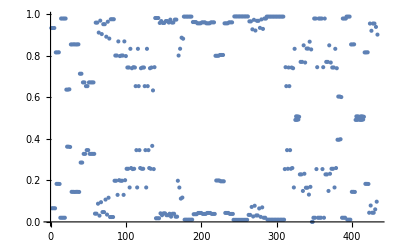
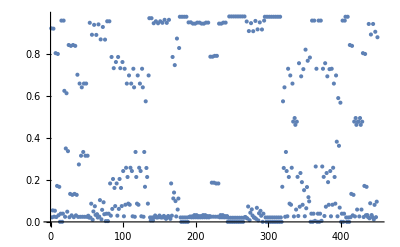
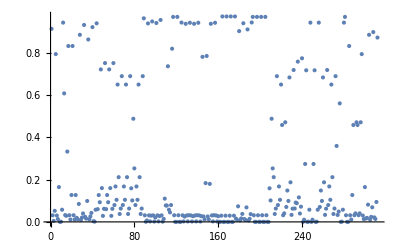
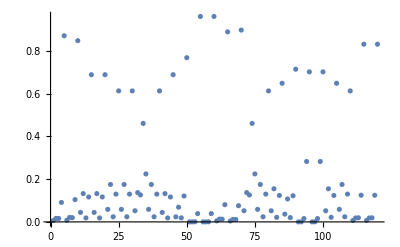
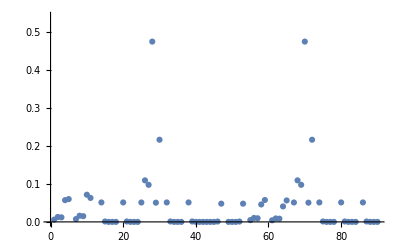
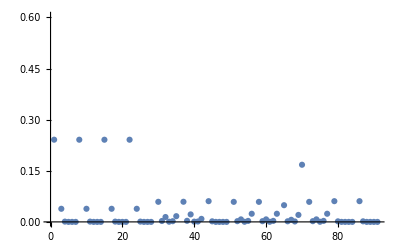

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

### Parameters

```mathematica
gamsModelName="liver-model-2";
```

```mathematica
gamsDir="gams";
```

### MID measurements

Metabolites with measured MIDs

```mathematica
measMetNames=metList⟦measuredIndex,1⟧
```

{glc-D,ala-L,arg-L,asp-L,gln-L,glu-L,gly,ser-L,mal-L,g3p,acrn,glyc3p,orn,citr-L}

Use the H_CE_LS_L experiment data group (2,4)

```mathematica
measMIDs=Table[
Transpose[mids[m]⟦All,2,4⟧],
{m,measMetNames}];
```

```mathematica
TableForm[Mean/@measMIDs,TableHeadings->{measMetNames,None}]
```

glc-D | 0.262317 | 0.0183042 | 0.00176102 | 0.00986813 | 0.00052536 | 0.0387348 | 0.66849
ala-L | 0.191648 | 0.0129476 | 0.0206615 | 0.774743 |  |  | 
arg-L | 0.365359 | 0.0218374 | 0.00380152 | 0. | 0. | 0.0658181 | 0.543184
asp-L | 0.257642 | 0.0685404 | 0.112236 | 0.038575 | 0.523006 |  | 
gln-L | 0.0421844 | 0.0126179 | 0.0111779 | 0.0290191 | 0.0277113 | 0.877289 | 
glu-L | 0.181092 | 0.0798193 | 0.0703866 | 0.179322 | 0.0194931 | 0.469887 | 
gly | 0.244932 | 0.0591931 | 0.695875 |  |  |  | 
ser-L | 0.330859 | 0.0962914 | 0.228475 | 0.344374 |  |  | 
mal-L | 0.304665 | 0.103519 | 0.14483 | 0.0701563 | 0.376831 |  | 
g3p | 0.731774 | 0.00127524 | 0.0288207 | 0.23813 |  |  | 
acrn | 0.854496 | 0.0820398 | 0.0634639 |  |  |  | 
glyc3p | 0.632577 | 0.0443948 | 0.0331205 | 0.289908 |  |  | 
orn | 0.207628 | 0.00934284 | 0. | 0. | 0.0277849 | 0.755244 | 
citr-L | 0.204204 | 0. | 0. | 0. | 0.0117464 | 0.774134 | 0.00991599

Standard deviations: we now assume the same standard deviation for all MIs of a metabolite --- change this!

```mathematica
TableForm[Max/@StandardDeviation/@measMIDs,TableHeadings->{measMetNames,None}]
```

glc-D | 0.0269153
ala-L | 0.0295438
arg-L | 0.124108
asp-L | 0.0653022
gln-L | 0.00965923
glu-L | 0.0347811
gly | 0.0262558
ser-L | 0.0637136
mal-L | 0.0219433
g3p | 0.109682
acrn | 0.00618417
glyc3p | 0.0191718
orn | 0.0293957
citr-L | 0.0340595

### Generate optimization model

```mathematica
(*SetDirectory[gamsDir]*)
```

```mathematica
experiments={"experiment1"};
```

Generate model, random starting point

```mathematica
GAMSExport[gamsDir,gamsModelName,net,
emuReactions,emuEq,irList,
First/@measuredFluxes,Last/@measuredFluxes,0.1(Last/@measuredFluxes),
experiments,measMetNames,{Mean/@measMIDs},{Max/@StandardDeviation/@measMIDs},
targets,emuMixing,
RandomFluxState[10]]
```

gams\liver-model-2.gms

For getting CIs

```mathematica
"FluxCI"->{"PGMT_f","ACS_f"}
```

```mathematica
Options[GAMSExport]
```

{FluxCI→{},FluxRatioCI→False,ConfidenceLevel→0.9,FixedFluxes→{},TestCase→False}

### Run GAMS

From command line ...

### Import GAMS solutions

#### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measMetNames,targets]
```

SparseArray[<17>, {14, 22}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{metList⟦measuredIndex⟦ij⟦All,1⟧⟧,1⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

glc-D | <glc-D_r{(123456)}> | 1.
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 1.
asp-L | <asp-L_c{(1234)}> | 1.
gln-L | <gln-L_m{(12345)}> | 1.
glu-L | <glu-L_c{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.
ser-L | <ser-L_c{(123)}> | 1.
mal-L | <mal-L_m{(1234)}> | 1.
g3p | <g3p_c{(123)}> | 1.
acrn | <acrn_c{(17)}> | 0.5
acrn | <acrn_m{(17)}> | 0.5
glyc3p | <glyc3p_c{(123)}> | 1.
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5

#### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

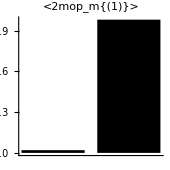
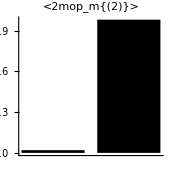
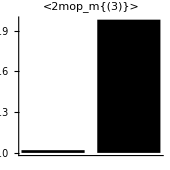
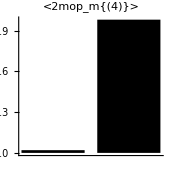
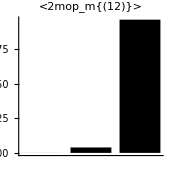
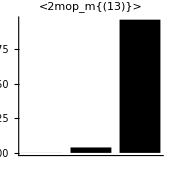
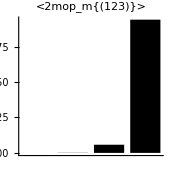

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["2mop",_,_],_]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

#### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixing;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

Compare fitted MIDs (gray) with measured (black)

NOTES:
M+3 in TCA cycle metabolites suggests propanoate entry from BCAA? Addition of propanoate-coa entry did not help ... for M+3 to also reach glutamate, AKGDm would have to be reversible. Other amino acids entering at akg?
Lower MIs in glutamine suggests some exchange with glutamate; for now I made glutaminase reversible
Higher M+0 in arginine than ornithine may reflect separate pools

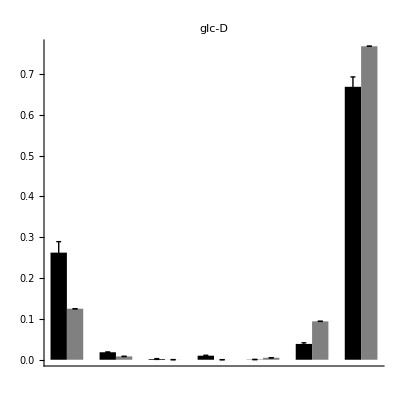
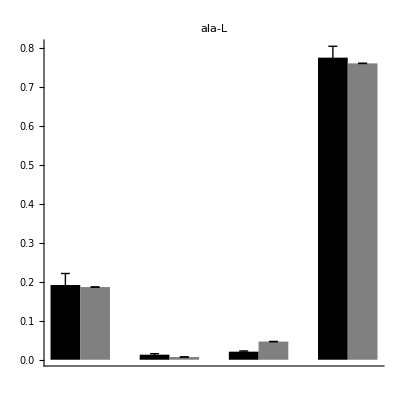
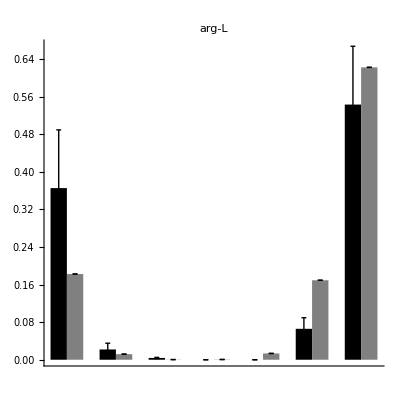
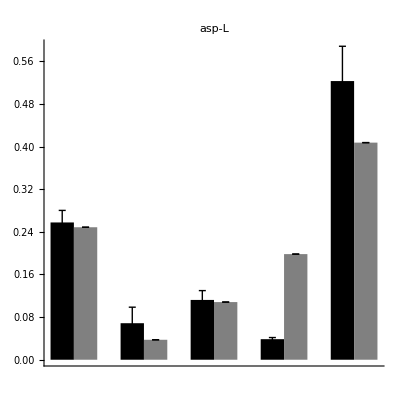
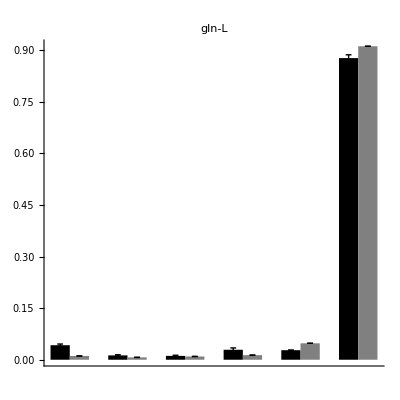
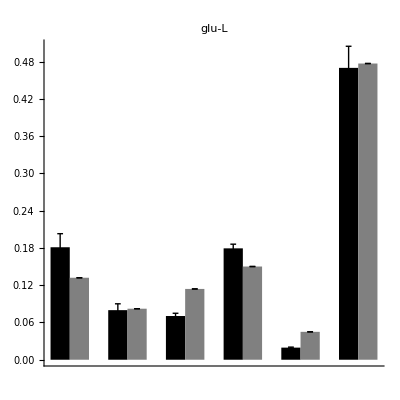
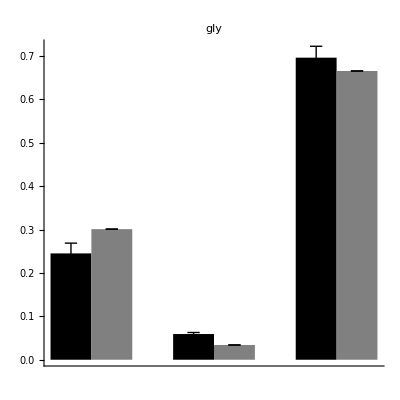
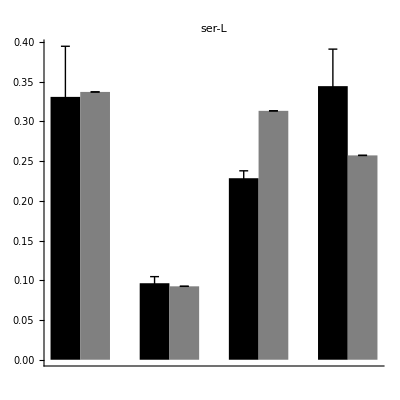

```mathematica
Table[
ErrorBarChart[
Transpose/@{measMIDs⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measMetNames⟦i⟧],
{i,Length[measMetNames]}]
```

OLD

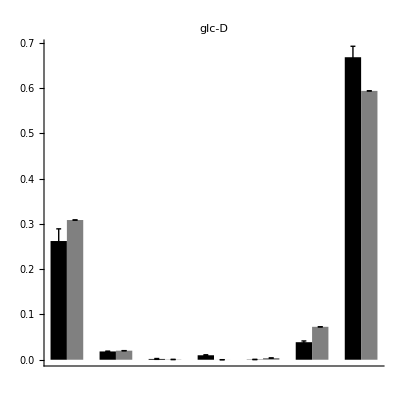
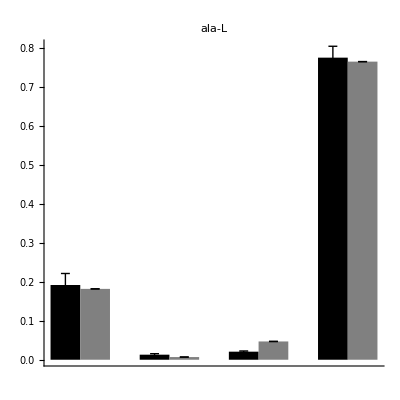
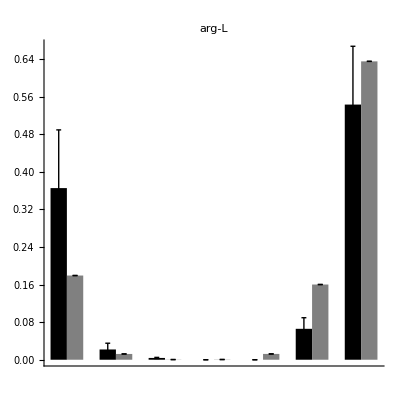
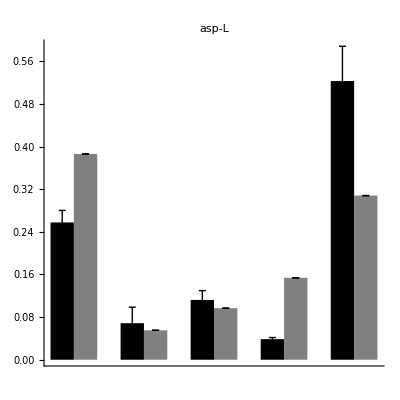
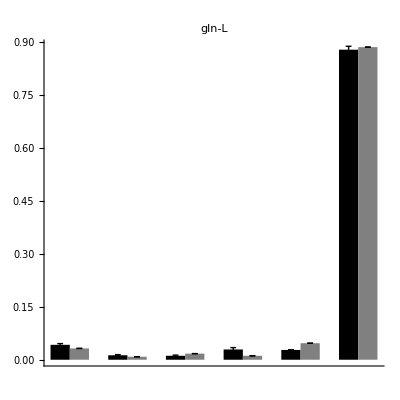
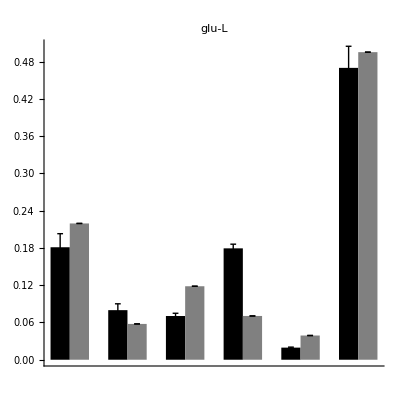
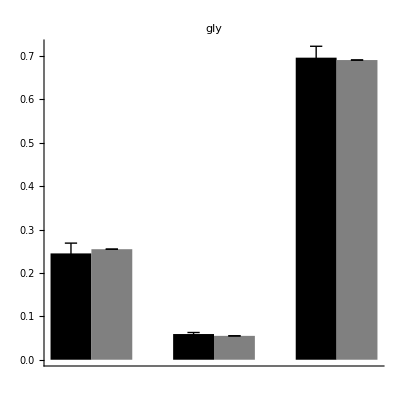
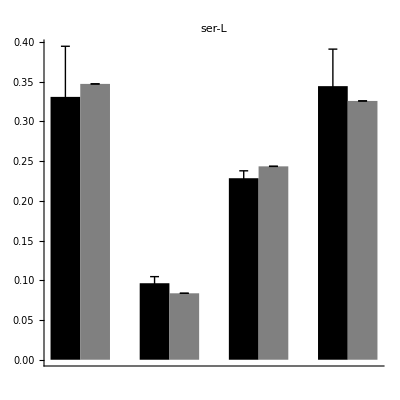

Scatter plot of all MIDs

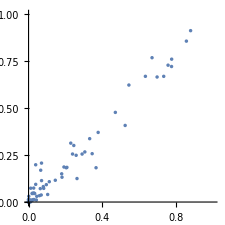

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@measMIDs],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

#### Fluxes

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 89 reactions, 35 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 2.40964 | 0. | 2.40964
<Reaction ACITL> | 3.48227 | 0. | 3.48227
<Reaction ACOAHi> | 0.001 | 0. | 0.001
<Reaction ACONTm(rev)> | 0.290231 | 0.001 | 0.289231
<Reaction ACRNtm> | 3.69916 | 0. | 3.69916
<Reaction ACS> | 0.217891 | 0. | 0.217891
<Reaction ADK1> | 0.260257 | 0. | 0.260257
<Reaction AKGDm(rev)> | 0.00200889 | 0.00200889 | 0.
<Reaction AKGtm(rev)> | 0.535205 | 0.001 | 0.534205
<Reaction ALATA_L> | 0.340654 | 0. | 0.340654
<Reaction ARGN> | 0.042366 | 0. | 0.042366
<Reaction ARGSL> | 0.042366 | 0. | 0.042366
<Reaction ARGSS> | 0.042366 | 0. | 0.042366
<Reaction ASPTA(rev)> | 1.65176 | 0.326322 | 1.32544
<Reaction ASPTAm(rev)> | 0.890057 | 0.001 | 0.889057
<Reaction ASPtm> | 0.889057 | 0. | 0.889057
<Reaction ATPS4m> | 6.06024 | 0. | 6.06024
<Reaction ATPtm(rev)> | 5.08936 | 0.001 | 5.08836
<Reaction CBPSam> | 0.042366 | 0. | 0.042366
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 3.48227 | 0. | 3.48227
<Reaction CO2tm(rev)> | 10000. | 9999.43 | 0.567939
<Reaction CRNtim> | 3.69916 | 0. | 3.69916
<Reaction CSm> | 3.7715 | 0. | 3.7715
<Reaction CSNATm> | 3.69916 | 0. | 3.69916
<Reaction CSNATr> | 3.69916 | 0. | 3.69916
<Reaction CYOOm> | 1.21225 | 0. | 1.21225
<Reaction CYOR-u10m> | 2.4245 | 0. | 2.4245
<Reaction ENO(rev)> | 10000. | 9999.44 | 0.557331
<Reaction FBA(rev)> | 0.28035 | 0.001 | 0.27935
<Reaction FBP> | 0.001 | 0. | 0.001
<Reaction FUMm> | 0.043366 | 0. | 0.043366
<Reaction FUMtm> | 0.042366 | 0. | 0.042366
<Reaction G3PD1(rev)> | 10000. | 9997.8 | 2.19893
<Reaction G6PPer> | 0.001 | 0. | 0.001
<Reaction G6Pter> | 0.001 | 0. | 0.001
<Reaction GAPD(rev)> | 10000. | 9997.24 | 2.75763
<Reaction GHMT2r(rev)> | 4.7303 | 4.7303 | 0.
<Reaction GLCter> | 0.001 | 0. | 0.001
<Reaction GLNtm> | 0.278305 | 0. | 0.278305
<Reaction GLUDxm(rev)> | 0.001 | 1.71349 | -1.71249
<Reaction GLUNm(rev)> | 0.333546 | 0.0552409 | 0.278305
<Reaction GLUt2m(rev)> | 33.0357 | 34.1374 | -1.10174
<Reaction GLYCOGEN_BREAK> | 0.0745993 | 0. | 0.0745993
<Reaction GLYK> | 2.19893 | 0. | 2.19893
<Reaction GTHS> | 1.71451 | 0. | 1.71451
<Reaction H2Oter> | 0.001 | 0. | 0.001
<Reaction H2Otm(rev)> | 0.001 | 5.17454 | -5.17354
<Reaction HCO3Em> | 0.93051 | 0. | 0.93051
<Reaction HEX1> | 0.205751 | 0. | 0.205751
<Reaction Htm2(rev)> | 14.3458 | 15.0513 | -0.705553
<Reaction ICDHxm(rev)> | 0.290231 | 0.001 | 0.289231
<Reaction LDH_L(rev)> | 3.4268 | 0.001 | 3.4258
<Reaction MALtm> | 3.73005 | 0. | 3.73005
<Reaction MDH> | 3.73005 | 0. | 3.73005
<Reaction MDHm(rev)> | 3.77442 | 0.001 | 3.77342
<Reaction MMEm> | 0.001 | 0. | 0.001
<Reaction MMMm> | 0.001 | 0. | 0.001
<Reaction MMSAD1m> | 0.001 | 0. | 0.001
<Reaction NADH2-u10m> | 2.4235 | 0. | 2.4235
<Reaction NADH_REDOX> | 0.001 | 0. | 0.001
<Reaction NDPK1> | 1.07766 | 0. | 1.07766
<Reaction NH4tm(rev)> | 12.6042 | 11.1276 | 1.47655
<Reaction O2tm> | 1.21225 | 0. | 1.21225
<Reaction OCBTm> | 0.042366 | 0. | 0.042366
<Reaction ORNt4m> | 0.042366 | 0. | 0.042366
<Reaction PCm> | 0.887144 | 0. | 0.887144
<Reaction PDHm> | 0.0723402 | 0. | 0.0723402
<Reaction PEPCK> | 1.07766 | 0. | 1.07766
<Reaction PFK> | 0.28035 | 0. | 0.28035
<Reaction PGCD> | 2.2003 | 0. | 2.2003
<Reaction PGI(rev)> | 0.28035 | 0.001 | 0.27935
<Reaction PGK(rev)> | 10000. | 9997.24 | 2.75763
<Reaction PGM(rev)> | 10000. | 9999.44 | 0.557331
<Reaction PGMT> | 0.0745993 | 0. | 0.0745993
<Reaction PIt2m> | 5.08836 | 0. | 5.08836
<Reaction PIter> | 0.001 | 0. | 0.001
<Reaction PPA> | 0.260257 | 0. | 0.260257
<Reaction PPCOACm> | 0.001 | 0. | 0.001
<Reaction PROTDEG_ALA> | 0.0655691 | 0. | 0.0655691
<Reaction PROTDEG_ARG> | 0.0556084 | 0. | 0.0556084
<Reaction PSERT> | 2.2003 | 0. | 2.2003
<Reaction PSP_L> | 2.2003 | 0. | 2.2003
<Reaction PYK> | 1.63499 | 0. | 1.63499
<Reaction PYRt2m(rev)> | 0.960484 | 0.001 | 0.959484
<Reaction SERHL> | 2.40964 | 0. | 2.40964
<Reaction SUCD1m> | 0.001 | 0. | 0.001
<Reaction SUCOASm> | 0.001 | 0. | 0.001
<Reaction TPI(rev)> | 10000. | 9997.52 | 2.47828

```mathematica
TableForm[BoundaryFlux[fluxGams],TableHeadings->{BoundaryFluxNames[bnet],None}]
```

2mop_IN | 0.001
ac_IN | 0.216891
ala-L_IN | 0.275085
arg-L_IN | 0.230161
asp-L_IN | 0.578226
co2_IN | 9999.49
energy_IN | 0.001
glc-D_IN | 1.
gln-L_IN | 0.278305
glucys_IN | 1.71451
gly_IN | 1.71451
glyc_IN | 2.19893
glycogen_IN | 0.0745993
h_IN | 30.5865
h2o_IN | 11.009
nh4_IN | 6.71048
o2_IN | 1.21225
pi_IN | 0.001
prot_ala_IN | 0.0655691
prot_arg_IN | 0.0556084
ser-L_IN | 0.210342
arg-L_OUT | 0.28577
asp-L_OUT | 0.0994813
co2_OUT | 10000.
energy_OUT | 0.002
glc-D_OUT | 0.795249
glu-L_OUT | 0.567536
gthrd_OUT | 1.71451
h_OUT | 32.9521
h2o_OUT | 14.233
lac-L_OUT | 3.4258
nh4_OUT | 7.64356
pi_OUT | 0.001
ser-L_OUT | 0.001
urea_OUT | 0.042366

List of nonzero metabolite balances

```mathematica
Cases[
Transpose[{MetaboliteShortName/@Metabolites[net],Chop[MassBalance[net,fluxGams],10^-6]}],
{_,Except[0]}]//TableForm
```

2mop_m | -0.001
ac_c | -0.216891
ala-L_c | -0.275085
arg-L_c | 0.0556084
asp-L_c | -0.478745
co2_c | 0.509719
energy_c | 0.001
glc-D_c | -0.204751
gln-L_c | -0.278305
glucys_c | -1.71451
glu-L_c | 0.567536
gly_c | -1.71451
glyc_c | -2.19893
glycogen_c | -0.0745993
gthrd_c | 1.71451
h_c | 2.36561
h2o_c | 3.22396
lac-L_c | 3.4258
nh4_c | 0.933084
o2_c | -1.21225
prot_ala_c | -0.0655691
prot_arg_c | -0.0556084
ser-L_c | -0.209342
urea_c | 0.042366

```mathematica
measuredFluxes
```

{ala-L_IN→1.91,asp-L_IN→0.55,arg-L_IN→0.23,glc-D_IN→1.,gln-L_IN→4.1,gly_IN→1.54,ser-L_IN→0.22,asp-L_OUT→0.1,glu-L_OUT→0.54}